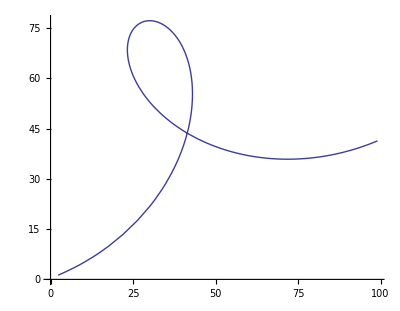

```mathematica
ParametricPlot[30({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2}]
```

```mathematica
Round[Table[30({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.1]
```

{{2.3,1.3},{13.1,6.9},{22.7,14.1},{30.6,22.5},{36.7,31.7},{40.7,41.2},{42.7,50.5},{42.8,58.9},{41.3,66.1},{38.6,71.7},{35.,75.4},{31.2,77.1},{27.7,76.7},{25.,74.5},{23.4,70.6},{23.6,65.5},{25.6,59.6},{29.6,53.5},{35.7,47.6},{43.6,42.4},{53.2,38.6},{64.,36.3},{75.6,36.},{87.4,37.6},{99.,41.3}}

```mathematica
StringJoin[("[NSValue valueWithPoint:NSMakePoint("<>ToString[#[[1]]]<>", "<>ToString[#[[2]]]<>")],\n")&/@Round[Table[30({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.1]]
```

[NSValue valueWithPoint:NSMakePoint(2.3, 1.3)],
[NSValue valueWithPoint:NSMakePoint(13.1, 6.9)],
[NSValue valueWithPoint:NSMakePoint(22.7, 14.1)],
[NSValue valueWithPoint:NSMakePoint(30.6, 22.5)],
[NSValue valueWithPoint:NSMakePoint(36.7, 31.7)],
[NSValue valueWithPoint:NSMakePoint(40.7, 41.2)],
[NSValue valueWithPoint:NSMakePoint(42.7, 50.5)],
[NSValue valueWithPoint:NSMakePoint(42.8, 58.9)],
[NSValue valueWithPoint:NSMakePoint(41.3, 66.1)],
[NSValue valueWithPoint:NSMakePoint(38.6, 71.7)],
[NSValue valueWithPoint:NSMakePoint(35., 75.4)],
[NSValue valueWithPoint:NSMakePoint(31.2, 77.1)],
[NSValue valueWithPoint:NSMakePoint(27.7, 76.7)],
[NSValue valueWithPoint:NSMakePoint(25., 74.5)],
[NSValue valueWithPoint:NSMakePoint(23.4, 70.6)],
[NSValue valueWithPoint:NSMakePoint(23.6, 65.5)],
[NSValue valueWithPoint:NSMakePoint(25.6, 59.6)],
[NSValue valueWithPoint:NSMakePoint(29.6, 53.5)],
[NSValue valueWithPoint:NSMakePoint(35.7, 47.6)],
[NSValue valueWithPoint:NSMakePoint(43.6, 42.4)],
[NSValue valueWithPoint:NSMakePoint(53.2, 38.6)],
[NSValue valueWithPoint:NSMakePoint(64., 36.3)],
[NSValue valueWithPoint:NSMakePoint(75.6, 36.)],
[NSValue valueWithPoint:NSMakePoint(87.4, 37.6)],
[NSValue valueWithPoint:NSMakePoint(99., 41.3)],